The data below correspond to the Laspeyres (base-1980), Paasche (base 2017) and Fisher-ideal)

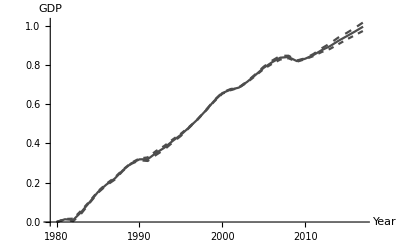

```mathematica
data={{1980,1.0000,1.0000,1.0000},{1981,1.0127,1.0154,1.0141},{1982,1.0044,1.0172,1.0108},{1983,1.0454,1.0614,1.0534},{1984,1.1028,1.1122,1.1075},{1985,1.1612,1.1701,1.1657},{1986,1.2050,1.2149,1.2100},{1987,1.2404,1.2535,1.2469},{1988,1.2977,1.3059,1.3018},{1989,1.3445,1.3513,1.3479},{1990,1.3696,1.3823,1.3760},{1991,1.3647,1.3896,1.3771},{1992,1.4075,1.4355,1.4214},{1993,1.4462,1.4735,1.4598},{1994,1.4999,1.5217,1.5108},{1995,1.5508,1.5678,1.5593},{1996,1.6163,1.6235,1.6199},{1997,1.6860,1.6850,1.6855},{1998,1.7664,1.7615,1.7640},{1999,1.8579,1.8455,1.8517},{2000,1.9346,1.9224,1.9285},{2001,1.9684,1.9568,1.9626},{2002,1.9844,1.9819,1.9831},{2003,2.0474,2.0362,2.0418},{2004,2.1226,2.1062,2.1144},{2005,2.2060,2.1805,2.1932},{2006,2.2741,2.2379,2.2559},{2007,2.3316,2.2879,2.3096},{2008,2.3326,2.3026,2.3175},{2009,2.2770,2.2627,2.2699},{2010,2.3022,2.2921,2.2971},{2011,2.3527,2.3285,2.3405},{2012,2.4222,2.3774,2.3997},{2013,2.4831,2.4149,2.4488},{2014,2.5584,2.4733,2.5155},{2015,2.6183,2.5332,2.5754},{2016,2.6870,2.5891,2.6376},{2017,2.7639,2.6475,2.7051}};

logData={#[[1]],Log[#[[2]]],Log[#[[3]]],Log[#[[4]]]}&/@data;

series1=logData[[All,{1,2}]];
series2=logData[[All,{1,3}]];
series3=logData[[All,{1,4}]];

ListLinePlot[{series1,series2,series3},PlotStyle->{Directive[GrayLevel[0.3],Dashed],Directive[GrayLevel[0.3],Dashing[{0.01,0.01}]],Directive[GrayLevel[0.3]]},AxesLabel->{"Year","GDP"},Ticks->{Range[1980,2017,5],Automatic},Joined->True,GridLines->None,PlotRange->All]
```